```mathematica
2+2
```

4

```mathematica
N[Pi,1000]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117067982148086513282306647093844609550582231725359408128481117450284102701938521105559644622948954930381964428810975665933446128475648233786783165271201909145648566923460348610454326648213393607260249141273724587006606315588174881520920962829254091715364367892590360011330530548820466521384146951941511609433057270365759591953092186117381932611793105118548074462379962749567351885752724891227938183011949129833673362440656643086021394946395224737190702179860943702770539217176293176752384674818467669405132000568127145263560827785771342757789609173637178721468440901224953430146549585371050792279689258923542019956112129021960864034418159813629774771309960518707211349999998372978049951059731732816096318595024459455346908302642522308253344685035261931188171010003137838752886587533208381420617177669147303598253490428755468731159562863882353787593751957781857780532171226806613001927876611195909216420199

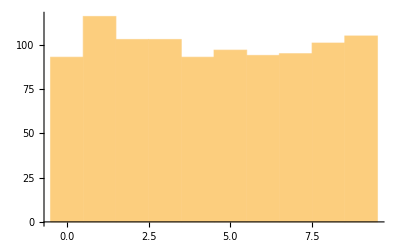

```mathematica
Histogram[First[RealDigits[Pi,10,1000]]]
```

```mathematica
Manipulate[Plot3D[Sin[x y+a],{x,0,3},{y,0,3}],{a,0,10}]
```

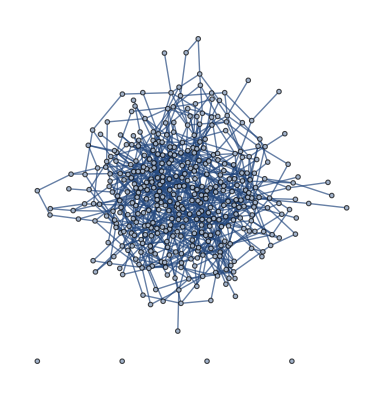

```mathematica
RandomGraph[{400,800}]
```

```mathematica
Manipulate[Graph[Table[i->Mod[i^2,n],{i,n}]],{n,2,200,1}]
```

```mathematica
CurrentImage[]
```

-Graphics-

```mathematica
ImageAssemble[Sort/@ImagePartition[-Graphics-,10]]
```

```mathematica
Dynamic[ImageAssemble[Sort/@ImagePartition[CurrentImage[],10]]]
```

```mathematica
Flatten[ImagePartition[-Graphics-,10]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

( FeatureSpacePlot requires Wolfram Language 11.1 )

```mathematica
FeatureSpacePlot[%]
```

-Graphics-

```mathematica
LinguisticAssistant["Population"]
```

8550405 people

```mathematica
GeoDistance[LinguisticAssistant,LinguisticAssistant]
```

9920.18 mi

```mathematica
LinguisticAssistant
```

{Tirana,Andorra la Vella,Vienna,Minsk,Brussels,Sarajevo,Sofia,Zagreb,Nicosia,Prague,Copenhagen,Tallinn,Torshavn,Helsinki,Paris,Berlin,Gibraltar,Athens,Saint Peter Port,Budapest,Reykjavik,Dublin,Douglas,Rome,Saint Helier,Pristina,Riga,Vaduz,Vilnius,Luxemburg,Skopje,Valletta,Chisinau,Monaco,Podgorica,Amsterdam,Oslo,Warsaw,Lisbon,Bucharest,San Marino,Belgrade,Bratislava,Ljubljana,Madrid,Longyearbyen,Stockholm,Bern,Kyiv,London,Vatican City}

```mathematica
GeoPosition[%]
```

GeoPosition[…]

```mathematica
FindShortestTour[%]
```

{14083. mi,{1,31,26,7,18,9,40,33,49,4,29,38,10,16,11,37,47,27,12,14,46,21,13,23,22,50,19,25,15,5,36,30,48,28,34,2,45,39,17,32,24,51,41,44,8,3,43,20,42,6,35,1}}

```mathematica
%14[[Last[%]]]
```

{Tirana,Skopje,Pristina,Sofia,Athens,Nicosia,Bucharest,Chisinau,Kyiv,Minsk,Vilnius,Warsaw,Prague,Berlin,Copenhagen,Oslo,Stockholm,Riga,Tallinn,Helsinki,Longyearbyen,Reykjavik,Torshavn,Douglas,Dublin,London,Saint Peter Port,Saint Helier,Paris,Brussels,Amsterdam,Luxemburg,Bern,Vaduz,Monaco,Andorra la Vella,Madrid,Lisbon,Gibraltar,Valletta,Rome,Vatican City,San Marino,Ljubljana,Zagreb,Vienna,Bratislava,Budapest,Belgrade,Sarajevo,Podgorica,Tirana}

```mathematica
GeoListPlot[%,Joined->True]
```

-Graphics-

```mathematica
GeoListPlot[%]
```

-Graphics-

```mathematica
LinguisticAssistant
```

{Albania,Andorra,Austria,Belarus,Belgium,Bosnia and Herzegovina,Bulgaria,Croatia,Czech Republic,Denmark,Estonia,Faroe Islands,Finland,France,Germany,Gibraltar,Greece,Guernsey,Hungary,Iceland,Ireland,Isle of Man,Italy,Jersey,Kosovo,Latvia,Liechtenstein,Lithuania,Luxembourg,Macedonia,Malta,Moldova,Monaco,Montenegro,Netherlands,Norway,Poland,Portugal,Romania,Russia,San Marino,Serbia,Slovakia,Slovenia,Spain,Svalbard,Sweden,Switzerland,Ukraine,United Kingdom,Vatican City}

```mathematica
EntityValue[%,"FlagImage"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

( FeatureSpacePlot requires Wolfram Language 11.1 )

```mathematica
FeatureSpacePlot[%10]
```

-Graphics-

```mathematica
ChromaticityPlot3D[%]
```

-Graphics3D-

```mathematica
WordTranslation["mathematics",All]
```

<|Mandarin→{數學},Hindi→{अंकगणित},Spanish→{matemáticas},Russian→{математика},Indonesian→{matematika},Portuguese→{matemática},Bengali→{গণিতশাস্ত্র},Arabic→{الرِّياضِيّات},Malay→{ilmu matematik},Japanese→{数学,数理},French→{mathématiques,math,maths},German→{Mathematik,Mathe},Urdu→{ریاضی},Javanese→{matematika},Turkish→{matematik},Telugu→{గణితము},Marathi→{गणितशास्त्र},Vietnamese→{toán học},Korean→{수학},Tamil→{கணக்கியல்},Thai→{คณิตศาสตร์},Italian→{matematica},Cantonese→{数学},Swahili→{hesabu},Gujarati→{ગણિતશાસ્ત્ર},Polish→{matematyka},Ukrainian→{математика},Hausa→{ilmin lissafi},Xiang Chinese→{suxio},Malayalam→{ഗണിതശാസ്തം},Kannada→{ಗಣಿತ},Burmese→{သင်္ချာအတတ်ပညာ},Oriya→{ଗଣିତ ଶାସ୍ତ୍ର},Hakka Chinese→{數學},Eastern Panjabi→{ریاضی},Sunda→{matematika},Bhojpuri→{गनित},Maithili→{गणित},South Azerbaijani→{riyaziyyat},Romanian→{matematică},Tagalog→{matematika},Dutch→{wiskunde},Sindhi→{علم رياضي، حسابي علم},Cebuano→{matematika},Igbo→{som,maasi},Amharic→{የሒሳብ ትምህርት},Nepali→{गणित},Assamese→{অঙ্কবিদ্যা},Hungarian→{matematika},Madura→{matematika},Central Khmer→{កនិតសាស្រ្ដ},Marwari→{गणित},Fulfulde Adamawa→{hisaabu},Magahi→{हिसाब},Somali→{xisaab},Greek→{μαθηματικά},Serbian→{matematika},Czech→{matematika},Shona→{masvomhu},Eastern Farsi→{ریاضیات,риёзиёт},Northern Zhuang→{suyoz},Zulu→{isayensi yezibalo},Nyanja→{masamu},Lombard→{matematiche},Belarusian→{матэматыка},Bulgarian→{математика},Swedish→{matematik,matte},Akan→{nkontaabuo},Kazakh→{математика},Ilocano→{matematika},Uyghur→{риязият},Rwanda→{Imibare},Xhosa→{imathematika},Hiligaynon→{matematika},Lingala→{zebi ya matematiki},Armenian→{մաթեմատիկա},Catalan-Valencian-Balear→{matemàtiques},Tatar→{математика},Minangkabau→{matematika},Turkmen→{matematika},Croatian→{matematika},Santali→{हिसब,गुणित},Afrikaans→{wiskunde},Danish→{matematik},Gikuyu→{mathabu},Finnish→{matematiikka},Hebrew→{מתמטיקה},Slovak→{matematika},Eastern Balochi→{حساب، رياضي},Rundi→{imibare},Norwegian→{matematikk},Kashmiri→{हिसाब,रियाज़ी},Central Tibetan→{ཨང་རྩིས་},Tswana→{dipalo},Basque→{matematika},Georgian→{მათემატიკა},Northern Sotho→{mathematiki},Wolof→{matematik},Central Bicolano→{matematika},Bugis→{matematika},Tsonga→{matematiki},Galician→{matemáticas},Eastern Yiddish→{מאטעמאטיק},Kirghiz→{математика},Lithuanian→{matematika},Aceh→{matematika},Kalenjin→{koilosiok},Zarma→{bayray guusu lasaabay ra},Esperanto→{matematiko},Slovenian→{matematika},Sidamo→{shallago},Bashkir→{математика},Chuvash→{математика},Swati→{sifundvo setibalo,imathemathiki},Makasar→{matematika},Macedonian→{математика},Gusii→{esabu},Ndebele→{iimbalo},Latvian→{matemātika},Tonga→{fika},Tumbuka→{masami},Teso→{esabu kere da akimara},Newar→{हिसाब},Breton→{jedoniezh},Estonian→{matemaatika},Scots→{eòlas tomhas is àireamh},Venda→{mbalo},Chechen→{математика},Mapudungun→{rakiduam},Maasai→{Mkisoma Naikenishoe},Erzya→{математика},Krio→{matematik},Fang→{metang},Kusaal→{gi'elug yєla},Karakalpak→{esap},Sango→{sènda-nômôrô},Efik→{ukpepnkpo abanade ibat},Aklanon→{matematika},Maltese→{matematika},Yakut→{математика},Samoan→{fika},Provençal→{matematico},Komi-Zyrian→{математика},Fijian→{vika},Icelandic→{stærðfræði},Papiamentu→{matemátika},Moksha→{математика},Kumyk→{математика},Navajo→{alhi'ayįįltaah},Maori→{paangarau},Gagauz→{matematika},Central Kaqchikel→{matemática},Dungan→{суанцүә},Kashubian→{matematika},Kaba→{matematik},Khakas→{математика},Akaselem→{isavu},Faroese→{støddfrøði},Ga'anda→{okubala},Romansch→{matematica},Evenki→{математика},Khanty→{математика},Chukot→{математика},Sanskrit→{अंकगणित},Nanai→{математика},Choctaw→{ná holhtina},Mansi→{математика},Koryak→{математика},Karaim→{хэсаб},Karon Dori→{математика},Bai→{merya},Batak→{matimatika},Gilyak→{математика},Alabama→{holtina},Judeo-Crimean Tatar→{хэсаб},Classical Quechua→{matemáticas}|>

```mathematica
First/@%
```

<|Mandarin→數學,Hindi→अंकगणित,Spanish→matemáticas,Russian→математика,Indonesian→matematika,Portuguese→matemática,Bengali→গণিতশাস্ত্র,Arabic→الرِّياضِيّات,Malay→ilmu matematik,Japanese→数学,French→mathématiques,German→Mathematik,Urdu→ریاضی,Javanese→matematika,Turkish→matematik,Telugu→గణితము,Marathi→गणितशास्त्र,Vietnamese→toán học,Korean→수학,Tamil→கணக்கியல்,Thai→คณิตศาสตร์,Italian→matematica,Cantonese→数学,Swahili→hesabu,Gujarati→ગણિતશાસ્ત્ર,Polish→matematyka,Ukrainian→математика,Hausa→ilmin lissafi,Xiang Chinese→suxio,Malayalam→ഗണിതശാസ്തം,Kannada→ಗಣಿತ,Burmese→သင်္ချာအတတ်ပညာ,Oriya→ଗଣିତ ଶାସ୍ତ୍ର,Hakka Chinese→數學,Eastern Panjabi→ریاضی,Sunda→matematika,Bhojpuri→गनित,Maithili→गणित,South Azerbaijani→riyaziyyat,Romanian→matematică,Tagalog→matematika,Dutch→wiskunde,Sindhi→علم رياضي، حسابي علم,Cebuano→matematika,Igbo→som,Amharic→የሒሳብ ትምህርት,Nepali→गणित,Assamese→অঙ্কবিদ্যা,Hungarian→matematika,Madura→matematika,Central Khmer→កនិតសាស្រ្ដ,Marwari→गणित,Fulfulde Adamawa→hisaabu,Magahi→हिसाब,Somali→xisaab,Greek→μαθηματικά,Serbian→matematika,Czech→matematika,Shona→masvomhu,Eastern Farsi→ریاضیات,Northern Zhuang→suyoz,Zulu→isayensi yezibalo,Nyanja→masamu,Lombard→matematiche,Belarusian→матэматыка,Bulgarian→математика,Swedish→matematik,Akan→nkontaabuo,Kazakh→математика,Ilocano→matematika,Uyghur→риязият,Rwanda→Imibare,Xhosa→imathematika,Hiligaynon→matematika,Lingala→zebi ya matematiki,Armenian→մաթեմատիկա,Catalan-Valencian-Balear→matemàtiques,Tatar→математика,Minangkabau→matematika,Turkmen→matematika,Croatian→matematika,Santali→हिसब,Afrikaans→wiskunde,Danish→matematik,Gikuyu→mathabu,Finnish→matematiikka,Hebrew→מתמטיקה,Slovak→matematika,Eastern Balochi→حساب، رياضي,Rundi→imibare,Norwegian→matematikk,Kashmiri→हिसाब,Central Tibetan→ཨང་རྩིས་,Tswana→dipalo,Basque→matematika,Georgian→მათემატიკა,Northern Sotho→mathematiki,Wolof→matematik,Central Bicolano→matematika,Bugis→matematika,Tsonga→matematiki,Galician→matemáticas,Eastern Yiddish→מאטעמאטיק,Kirghiz→математика,Lithuanian→matematika,Aceh→matematika,Kalenjin→koilosiok,Zarma→bayray guusu lasaabay ra,Esperanto→matematiko,Slovenian→matematika,Sidamo→shallago,Bashkir→математика,Chuvash→математика,Swati→sifundvo setibalo,Makasar→matematika,Macedonian→математика,Gusii→esabu,Ndebele→iimbalo,Latvian→matemātika,Tonga→fika,Tumbuka→masami,Teso→esabu kere da akimara,Newar→हिसाब,Breton→jedoniezh,Estonian→matemaatika,Scots→eòlas tomhas is àireamh,Venda→mbalo,Chechen→математика,Mapudungun→rakiduam,Maasai→Mkisoma Naikenishoe,Erzya→математика,Krio→matematik,Fang→metang,Kusaal→gi'elug yєla,Karakalpak→esap,Sango→sènda-nômôrô,Efik→ukpepnkpo abanade ibat,Aklanon→matematika,Maltese→matematika,Yakut→математика,Samoan→fika,Provençal→matematico,Komi-Zyrian→математика,Fijian→vika,Icelandic→stærðfræði,Papiamentu→matemátika,Moksha→математика,Kumyk→математика,Navajo→alhi'ayįįltaah,Maori→paangarau,Gagauz→matematika,Central Kaqchikel→matemática,Dungan→суанцүә,Kashubian→matematika,Kaba→matematik,Khakas→математика,Akaselem→isavu,Faroese→støddfrøði,Ga'anda→okubala,Romansch→matematica,Evenki→математика,Khanty→математика,Chukot→математика,Sanskrit→अंकगणित,Nanai→математика,Choctaw→ná holhtina,Mansi→математика,Koryak→математика,Karaim→хэсаб,Karon Dori→математика,Bai→merya,Batak→matimatika,Gilyak→математика,Alabama→holtina,Judeo-Crimean Tatar→хэсаб,Classical Quechua→matemáticas|>

```mathematica
StringTake[#,1]&/@%%
```

<|Mandarin→{數},Hindi→{अ},Spanish→{m},Russian→{м},Indonesian→{m},Portuguese→{m},Bengali→{গ},Arabic→{ا},Malay→{i},Japanese→{数,数},French→{m,m,m},German→{M,M},Urdu→{ر},Javanese→{m},Turkish→{m},Telugu→{గ},Marathi→{ग},Vietnamese→{t},Korean→{수},Tamil→{க},Thai→{ค},Italian→{m},Cantonese→{数},Swahili→{h},Gujarati→{ગ},Polish→{m},Ukrainian→{м},Hausa→{i},Xiang Chinese→{s},Malayalam→{ഗ},Kannada→{ಗ},Burmese→{သ},Oriya→{ଗ},Hakka Chinese→{數},Eastern Panjabi→{ر},Sunda→{m},Bhojpuri→{ग},Maithili→{ग},South Azerbaijani→{r},Romanian→{m},Tagalog→{m},Dutch→{w},Sindhi→{ع},Cebuano→{m},Igbo→{s,m},Amharic→{የ},Nepali→{ग},Assamese→{অ},Hungarian→{m},Madura→{m},Central Khmer→{ក},Marwari→{ग},Fulfulde Adamawa→{h},Magahi→{ह},Somali→{x},Greek→{μ},Serbian→{m},Czech→{m},Shona→{m},Eastern Farsi→{ر,р},Northern Zhuang→{s},Zulu→{i},Nyanja→{m},Lombard→{m},Belarusian→{м},Bulgarian→{м},Swedish→{m,m},Akan→{n},Kazakh→{м},Ilocano→{m},Uyghur→{р},Rwanda→{I},Xhosa→{i},Hiligaynon→{m},Lingala→{z},Armenian→{մ},Catalan-Valencian-Balear→{m},Tatar→{м},Minangkabau→{m},Turkmen→{m},Croatian→{m},Santali→{ह,ग},Afrikaans→{w},Danish→{m},Gikuyu→{m},Finnish→{m},Hebrew→{מ},Slovak→{m},Eastern Balochi→{ح},Rundi→{i},Norwegian→{m},Kashmiri→{ह,र},Central Tibetan→{ཨ},Tswana→{d},Basque→{m},Georgian→{მ},Northern Sotho→{m},Wolof→{m},Central Bicolano→{m},Bugis→{m},Tsonga→{m},Galician→{m},Eastern Yiddish→{מ},Kirghiz→{м},Lithuanian→{m},Aceh→{m},Kalenjin→{k},Zarma→{b},Esperanto→{m},Slovenian→{m},Sidamo→{s},Bashkir→{м},Chuvash→{м},Swati→{s,i},Makasar→{m},Macedonian→{м},Gusii→{e},Ndebele→{i},Latvian→{m},Tonga→{f},Tumbuka→{m},Teso→{e},Newar→{ह},Breton→{j},Estonian→{m},Scots→{e},Venda→{m},Chechen→{м},Mapudungun→{r},Maasai→{M},Erzya→{м},Krio→{m},Fang→{m},Kusaal→{g},Karakalpak→{e},Sango→{s},Efik→{u},Aklanon→{m},Maltese→{m},Yakut→{м},Samoan→{f},Provençal→{m},Komi-Zyrian→{м},Fijian→{v},Icelandic→{s},Papiamentu→{m},Moksha→{м},Kumyk→{м},Navajo→{a},Maori→{p},Gagauz→{m},Central Kaqchikel→{m},Dungan→{с},Kashubian→{m},Kaba→{m},Khakas→{м},Akaselem→{i},Faroese→{s},Ga'anda→{o},Romansch→{m},Evenki→{м},Khanty→{м},Chukot→{м},Sanskrit→{अ},Nanai→{м},Choctaw→{n},Mansi→{м},Koryak→{м},Karaim→{х},Karon Dori→{м},Bai→{m},Batak→{m},Gilyak→{м},Alabama→{h},Judeo-Crimean Tatar→{х},Classical Quechua→{m}|>

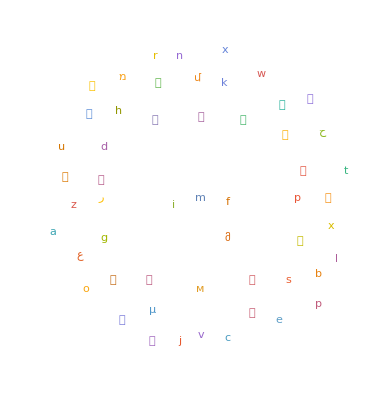

```mathematica
WordCloud[Values[%]]
```

```mathematica
Transliterate[Values[%%]]
```

{shu,a,m,m,m,m,ga,a,i,shu,m,M,r,m,m,ga,ga,t,su,ka,kh,m,shu,h,ga,m,m,i,s,ga,ga,သ,ga,shu,r,m,ga,ga,r,m,m,w,ʿ,m,s,የ,ga,a,m,m,ក,ga,h,ha,x,m,m,m,m,r,s,i,m,m,m,m,m,n,m,m,r,I,i,m,z,m,m,m,m,m,m,ha,w,m,m,m,m,m,h,i,m,ha,ཨ,d,m,m,m,m,m,m,m,m,m,m,m,m,k,b,m,m,s,m,m,s,m,m,e,i,m,f,m,e,ha,j,m,e,m,m,r,M,m,m,m,g,e,s,u,m,m,m,f,m,m,v,s,m,m,m,a,p,m,m,s,m,m,m,i,s,o,m,m,m,m,a,m,n,m,m,h,m,m,m,m,h,h,m}

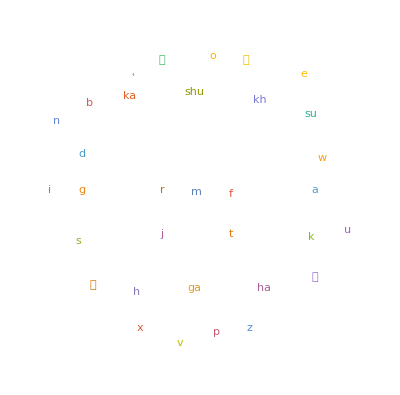

```mathematica
WordCloud[%]
```

## Our Math Experiment

```mathematica
PadLeft[IntegerDigits[NestList[FromDigits[Reverse[IntegerDigits[#]]]+#&,123,100]]]//ArrayPlot
```

-Graphics-

```mathematica
RotateLeft[{a,b,c,d}]
```

{b,c,d,a}

```mathematica
IntegerDigits[6746,2]
```

{1,1,0,1,0,0,1,0,1,1,0,1,0}

```mathematica
NestList[FromDigits[RotateLeft[IntegerDigits[#,2]],2]+#&,123,10]
```

{123,242,471,902,1683,3002,4911,6542,11435,17922,20999}

```mathematica
NestList[FromDigits[RotateLeft[IntegerDigits[#,2]],2]+#&,1,10]
```

{1,2,3,6,11,18,23,38,51,90,143}

```mathematica
FindSequenceFunction[%]
```

FindSequenceFunction[{1,2,3,6,11,18,23,38,51,90,143}]

```mathematica
PadLeft[IntegerDigits[NestList[FromDigits[RotateLeft[IntegerDigits[#,2]],2]+#&,1,1000],2]]//ArrayPlot
```

-Graphics-

```mathematica
Table[PadLeft[IntegerDigits[NestList[FromDigits[RotateLeft[IntegerDigits[#,2]],2]+#&,n,100],2]]//ArrayPlot,{n,20}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[PadLeft[IntegerDigits[NestList[FromDigits[RotateRight[IntegerDigits[#,2]],2]+#&,n,100],2]]//ArrayPlot,{n,20}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[PadLeft[IntegerDigits[NestList[Mod[FromDigits[RotateRight[IntegerDigits[#,2]],2],2^20]+#&,n,100],2]]//ArrayPlot,{n,20}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
With[{n=5},Range[0,2^n-1]]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31}

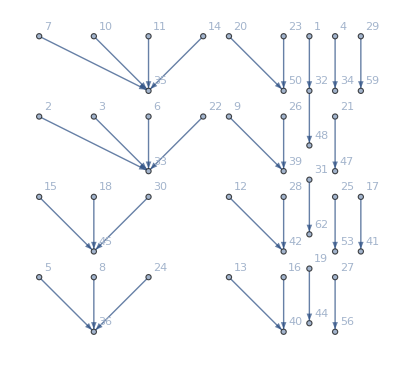

```mathematica
Graph[With[{n=5},#->Mod[FromDigits[RotateRight[IntegerDigits[#,2]],2],+#,2^n]&/@Range[2^n]],VertexLabels->Automatic]
```

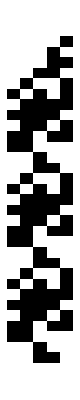
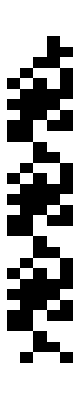
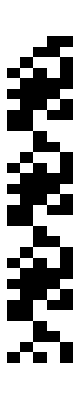
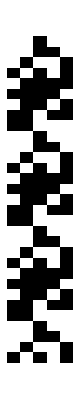
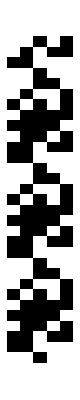
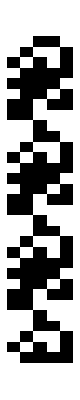
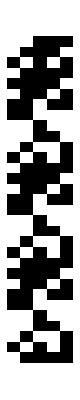
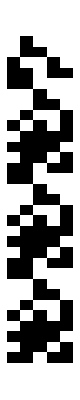

```mathematica
Table[PadLeft[IntegerDigits[NestList[Mod[FromDigits[RotateRight[IntegerDigits[#,2]],2]+#,2^5]&,n,30],2]]//ArrayPlot,{n,20}]
```

```mathematica
NestList[Mod[FromDigits[RotateRight[IntegerDigits[#,2]],2]+#,2^5]&,1,300]
```

{1,2,3,6,9,21,15,30,13,27,24,4,6,9,21,15,30,13,27,24,4,6,9,21,15,30,13,27,24,4,6,9,21,15,30,13,27,24,4,6,9,21,15,30,13,27,24,4,6,9,21,15,30,13,27,24,4,6,9,21,15,30,13,27,24,4,6,9,21,15,30,13,27,24,4,6,9,21,15,30,13,27,24,4,6,9,21,15,30,13,27,24,4,6,9,21,15,30,13,27,24,4,6,9,21,15,30,13,27,24,4,6,9,21,15,30,13,27,24,4,6,9,21,15,30,13,27,24,4,6,9,21,15,30,13,27,24,4,6,9,21,15,30,13,27,24,4,6,9,21,15,30,13,27,24,4,6,9,21,15,30,13,27,24,4,6,9,21,15,30,13,27,24,4,6,9,21,15,30,13,27,24,4,6,9,21,15,30,13,27,24,4,6,9,21,15,30,13,27,24,4,6,9,21,15,30,13,27,24,4,6,9,21,15,30,13,27,24,4,6,9,21,15,30,13,27,24,4,6,9,21,15,30,13,27,24,4,6,9,21,15,30,13,27,24,4,6,9,21,15,30,13,27,24,4,6,9,21,15,30,13,27,24,4,6,9,21,15,30,13,27,24,4,6,9,21,15,30,13,27,24,4,6,9,21,15,30,13,27,24,4,6,9,21,15,30,13,27,24,4,6}

```mathematica
FindTransientRepeat[%,4]
```

{{1,2,3},{6,9,21,15,30,13,27,24,4}}

```mathematica
#->Mod[FromDigits[RotateRight[IntegerDigits[#,2]],2]+#,2^5]&/@Range[2^5]
```

{1→2,2→3,3→6,4→6,5→11,6→9,7→14,8→12,9→21,10→15,11→24,12→18,13→27,14→21,15→30,16→24,17→9,18→27,19→12,20→30,21→15,22→1,23→18,24→4,25→21,26→7,27→24,28→10,29→27,30→13,31→30,32→16}

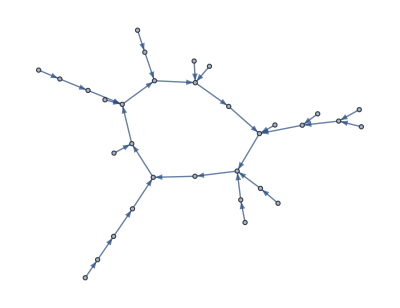

```mathematica
Graph[%]
```

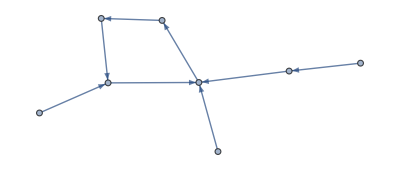
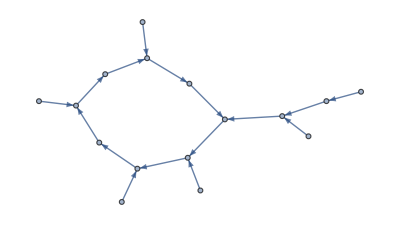
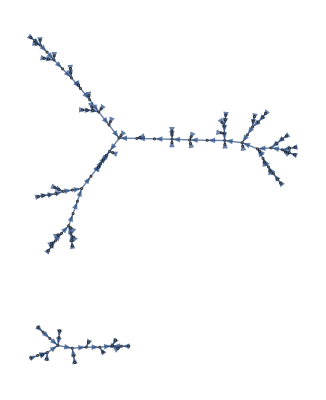
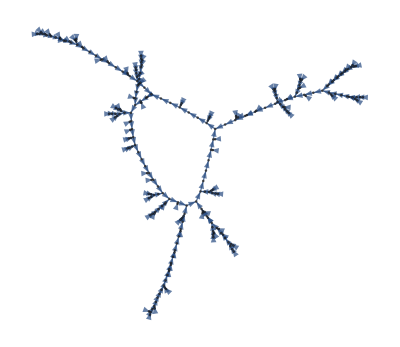
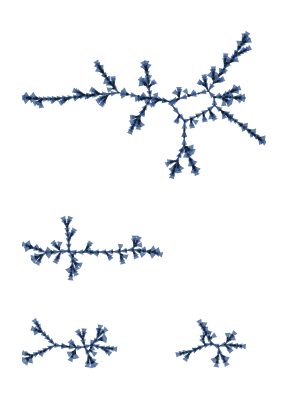
{-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-5,-Graphics-6,-Graphics-7,-Graphics-8,-Graphics-9,-Graphics-10}

```mathematica
Table[Labeled[Graph[#->Mod[FromDigits[RotateRight[IntegerDigits[#,2]],2]+#,2^n]&/@Range[2^n]],n],{n,2,10}]
```

```mathematica
Table[FindTransientRepeat[NestList[Mod[FromDigits[RotateRight[IntegerDigits[#,2]],2]+#,2^n]&,1,1000],4],{n,8}]//Column
```

{{1},{0}}
{{1},{2,3}}
{{},{1,2,3,6}}
{{1},{2,3,6,9,5,11,8,12}}
{{1,2,3},{6,9,21,15,30,13,27,24,4}}
{{1,2,3,6,9,21},{47,38,57,53}}
{{1,2,3,6,9,21,47},{102,25,53,111}}
{{1,2,3,6,9,21,47,102,153,101,215,194,35},{84,126,189,155,104,156,234,95,206,53,111,230,89,197,167,122,183,146,219,200,44,66,99,212,62,93,203,176,8,12,18,27,56}}

```mathematica
PadLeft[IntegerDigits[NestList[Mod[FromDigits[RotateRight[IntegerDigits[#,2]],2]+#,2^7]&,102,30],2]]//ArrayPlot
```

-Graphics-

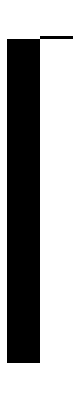
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[PadLeft[IntegerDigits[NestList[FromDigits[RotateLeft[IntegerDigits[#,2]],2]+n&,1,100],2]]//ArrayPlot,{n,20}]
```

```mathematica
Table[PadLeft[IntegerDigits[NestList[2FromDigits[RotateLeft[IntegerDigits[#,2]],2]+n&,1,100],2]]//ArrayPlot,{n,20}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Length/@Table[Last[PadLeft[IntegerDigits[NestList[2FromDigits[RotateLeft[IntegerDigits[#,2]],2]+n&,1,100],2]]],{n,20}]
```

{101,3,4,102,5,4,102,5,6,103,6,6,103,5,6,103,7,6,103,7}

```mathematica
Table[PadLeft[IntegerDigits[NestList[3FromDigits[RotateLeft[IntegerDigits[#,2]],2]+n&,1,100],2]]//ArrayPlot,{n,20}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[PadLeft[IntegerDigits[NestList[3(FromDigits[RotateLeft[IntegerDigits[#,2]],2]+n)+1&,1,100],2]]//ArrayPlot,{n,20}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Labeled[PadLeft[IntegerDigits[NestList[a FromDigits[RotateLeft[IntegerDigits[#,2]],2]+1&,1,100],2]]//ArrayPlot,a],{a,50}]
```

{-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-5,-Graphics-6,-Graphics-7,-Graphics-8,-Graphics-9,-Graphics-10,-Graphics-11,-Graphics-12,-Graphics-13,-Graphics-14,-Graphics-15,-Graphics-16,-Graphics-17,-Graphics-18,-Graphics-19,-Graphics-20,-Graphics-21,-Graphics-22,-Graphics-23,-Graphics-24,-Graphics-25,-Graphics-26,-Graphics-27,-Graphics-28,-Graphics-29,-Graphics-30,-Graphics-31,-Graphics-32,-Graphics-33,-Graphics-34,-Graphics-35,-Graphics-36,-Graphics-37,-Graphics-38,-Graphics-39,-Graphics-40,-Graphics-41,-Graphics-42,-Graphics-43,-Graphics-44,-Graphics-45,-Graphics-46,-Graphics-47,-Graphics-48,-Graphics-49,-Graphics-50}

```mathematica
Table[PadLeft[IntegerDigits[NestList[a FromDigits[RotateLeft[IntegerDigits[#,2]],2]+1&,1,100],2]]//Image,{a,50}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

( FeatureSpacePlot requires Wolfram Language 11.1 )

```mathematica
FeatureSpacePlot[%]
```

-Graphics-

```mathematica
imags=Table[PadLeft[IntegerDigits[NestList[a FromDigits[RotateLeft[IntegerDigits[#,2]],2]+1&,1,100],2]]//Image,{a,50}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Entropy[-Graphics-]
```

0.568001

```mathematica
Entropy/@imags
```

{0.693147,0.693098,0.636514,0.639531,0.566397,0.693098,0.562335,0.566397,0.574795,0.691684,0.45499,0.660286,0.562216,0.577144,0.500402,0.504789,0.559437,0.609933,0.566423,0.565865,0.58424,0.566867,0.380995,0.677831,0.569977,0.55437,0.574827,0.604015,0.560503,0.570745,0.450561,0.45499,0.566804,0.565707,0.540721,0.519015,0.545095,0.561511,0.56543,0.601298,0.556329,0.576333,0.520386,0.565917,0.548021,0.526239,0.329012,0.676069,0.568001,0.568467}

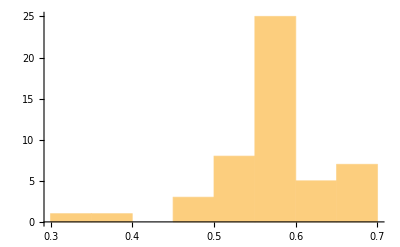

```mathematica
Histogram[%]
```

```mathematica
Image[Abs[Fourier[ImageData[-Graphics-]]]]
```

-Graphics-

```mathematica
Counts[Flatten[Partition[PadLeft[IntegerDigits[NestList[13 FromDigits[RotateLeft[IntegerDigits[#,2]],2]+1&,1,20],2]],{2,2}],1]]
```

<|{{0,0},{0,0}}→132,{{0,0},{0,1}}→13,{{0,0},{1,1}}→3,{{0,0},{1,0}}→4,{{0,1},{0,0}}→6,{{0,1},{1,0}}→5,{{0,1},{0,1}}→14,{{1,1},{0,0}}→4,{{1,0},{0,1}}→3,{{1,0},{1,1}}→8,{{1,0},{1,0}}→18,{{1,1},{1,1}}→11,{{1,0},{0,0}}→2,{{1,1},{0,1}}→4,{{1,1},{1,0}}→1,{{0,1},{1,1}}→2|>

```mathematica
Counts[Flatten[Partition[PadLeft[IntegerDigits[NestList[5 FromDigits[RotateLeft[IntegerDigits[#,2]],2]+1&,1,20],2]],{2,2}],1]]
```

<|{{0,0},{0,0}}→100,{{0,0},{1,1}}→10,{{1,1},{0,1}}→9,{{0,1},{0,1}}→81|>

```mathematica
Table[Length[Union[Flatten[Partition[PadLeft[IntegerDigits[NestList[a FromDigits[RotateLeft[IntegerDigits[#,2]],2]+1&,1,20],2]],{2,2}],1]]],{a,20}]
```

{2,3,2,6,4,7,4,3,11,8,6,4,16,12,3,6,16,9,16,9}

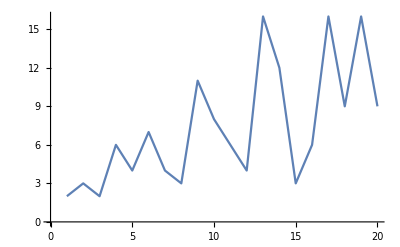

```mathematica
ListLinePlot[%]
```

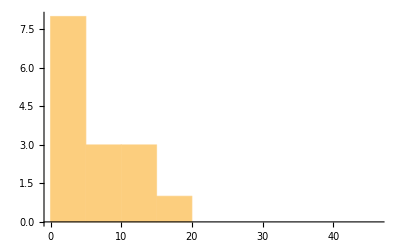

```mathematica
Histogram[Values[%62]]
```

```mathematica
Table[Length[Union[Flatten[Partition[PadLeft[IntegerDigits[NestList[a FromDigits[RotateLeft[IntegerDigits[#,2]],2]+1&,1,20],2]],{2,2}],1]]],{a,50}]
```

{2,3,2,6,4,7,4,3,11,8,6,4,16,12,3,6,16,9,16,9,16,16,4,8,16,16,16,15,16,15,4,3,16,15,16,15,16,16,16,15,16,16,16,15,16,16,6,7,16,16}

```mathematica
Position[%,16]
```

{{13},{17},{19},{21},{22},{25},{26},{27},{29},{33},{35},{37},{38},{39},{41},{42},{43},{45},{46},{49},{50}}

```mathematica
Flatten[%]
```

{13,17,19,21,22,25,26,27,29,33,35,37,38,39,41,42,43,45,46,49,50}

```mathematica
FindSequenceFunction[%]
```

FindSequenceFunction[{13,17,19,21,22,25,26,27,29,33,35,37,38,39,41,42,43,45,46,49,50}]

```mathematica
Differences[%%]
```

{4,2,2,1,3,1,1,2,4,2,2,1,1,2,1,1,2,1,3,1}

```mathematica
Table[Length[Union[Flatten[Partition[PadLeft[IntegerDigits[NestList[a FromDigits[RotateLeft[IntegerDigits[#,2]],2]+1&,1,20],2]],{2,2}],1]]],{a,1000}]
```

{2,3,2,6,4,7,4,3,11,8,6,4,16,12,3,6,16,9,16,9,16,16,4,8,16,16,16,15,16,15,4,3,16,15,16,15,16,16,16,15,16,16,16,15,16,16,6,7,16,16,16,16,16,16,16,15,16,16,16,16,16,16,3,6,16,16,16,16,16,16,16,16,16,16,16,9,16,16,16,10,16,16,16,16,16,16,16,15,16,16,16,16,16,16,4,10,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,4,3,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,14,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,14,16,16,16,16,16,16,16,15,16,16,16,16,16,16,6,10,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,3,6,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,15,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,12,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,4,9,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,14,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,4,3,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,15,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,12,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,9,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,6,10,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,15,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16}

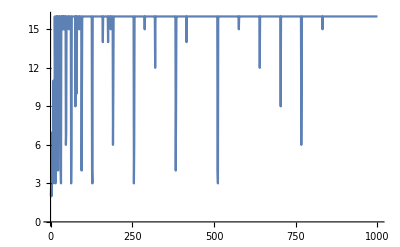

```mathematica
ListLinePlot[%]
```